```mathematica
ClearAll["Global`*"]
A=21.6
```

21.6

```mathematica
(*so definiert man die ganzzahlige Bedingung
h[l_,m_]= Sqrt[l(4m^2/l^2 -1)+l/4] /; {m ∈ PositiveIntegers,l∈ PositiveIntegers}*)
```

```mathematica
(*Check resonant conditions for NV-14N System:*)
f[k_,l_]:=A/(Sqrt[(1/4)*((4*k^2/(l^2))-1)] )
```

```mathematica
??f
```

```mathematica
g[m_,l_]:=A/(Sqrt[((4*m^2/(l^2))-1)] )
```

```mathematica
??g
```

```mathematica
(*Values for the ratio A/B1 for different values for l,k,m. f and g are resonant conditions for both detuned transitions, the first with 2A, the other with A. A = 2.2 MHz for 14N. If f=g, all conditions are fulfilled. l is the integer for the rotation of the electron spin and k, m are the integers for the rotation of the two detuned transitions. Typical values for the currently used weak drive are in the kHz range*)
l=1;
n=1;
l1=N[Table[{f[k,l],k},{k,1,20}]]
l2=N[Table[{g[m,l],m},{m,1,20}]]
b1sync=Intersection[l1[[All,1]],l2[[All,1]],SameTest->(Floor[#1,.1]==Floor[#2,.1]&)]
```

{{24.9415,1.},{11.1542,2.},{7.30213,3.},{5.44269,4.},{4.34176,5.},{3.61257,6.},{3.09362,7.},{2.70529,8.},{2.40371,9.},{2.16271,10.},{1.96567,11.},{1.80156,12.},{1.66277,13.},{1.54384,14.},{1.4408,15.},{1.35066,16.},{1.27114,17.},{1.20046,18.},{1.13724,19.},{1.08034,20.}}

{{12.4708,1.},{5.5771,2.},{3.65107,3.},{2.72134,4.},{2.17088,5.},{1.80628,6.},{1.54681,7.},{1.35264,8.},{1.20186,9.},{1.08135,10.},{0.982834,11.},{0.900782,12.},{0.831384,13.},{0.771921,14.},{0.7204,15.},{0.67533,16.},{0.635569,17.},{0.600232,18.},{0.568618,19.},{0.540169,20.}}

{1.08034,1.27114,1.35066,1.54384,1.80156,2.16271,2.70529,3.61257}

```mathematica
Favf[b1_,m_,k_]:=1/7+2/21 Cos[m π]^2 Cos[(√(A^2+b1^2) n π)/(2 b1)]^2+4/21 Cos[k π] Cos[m π] Cos[(√(A^2+b1^2) n π)/(2 b1)] Cos[(√(4 A^2+b1^2) n π)/(2 b1)]+2/21 Cos[k π]^2 Cos[(√(4 A^2+b1^2) n π)/(2 b1)]^2+2/21 Cos[(√(4 A^2+b1^2) n π)/(2 b1)]^2 Sin[k π]^2+4/21 Cos[(√(A^2+b1^2) n π)/(2 b1)] Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[m π]+2/21 Cos[(√(A^2+b1^2) n π)/(2 b1)]^2 Sin[m π]^2-4/21 Cos[m π] Cos[n π] Cos[(√(A^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]-4/21 Cos[k π] Cos[n π] Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]+2/21 Cos[n π]^2 Sin[(n π)/2]^2-4/21 Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[(n π)/2] Sin[n π]-4/21 Cos[(√(A^2+b1^2) n π)/(2 b1)] Sin[m π] Sin[(n π)/2] Sin[n π]+2/21 Sin[(n π)/2]^2 Sin[n π]^2;
```

```mathematica
localMax1=FindMaximum[{Favf[b1,8,16],1<=b1<=1.1},{b1,1.0803376582855675}]
localMax2=FindMaximum[{Favf[b1,7,16],1.2<=b1<=1.3},{b1,1.2711381544868392}]
localMax3=FindMaximum[{Favf[b1,8,16],1.3<=b1<=1.4},{b1,1.3506596628783605}]
localMax4=FindMaximum[{Favf[b1,7,16],1.5<=b1<=1.6},{b1,1.5438420501664245}]
localMax5=FindMaximum[{Favf[b1,8,16],1.7<=b1<=1.85},{b1,1.8015645374531262}]
localMax6=FindMaximum[{Favf[b1,7,16],2.1<=b1<=2.18},{b1,2.1627050730699984}]
localMax7=FindMaximum[{Favf[b1,8,16],2.65<=b1<=2.75},{b1,2.7052889374878464}]
localMax8=FindMaximum[{Favf[b1,7,16],3.5<=b1<=3.7},{b1,3.6125654832306324}]
```

{0.999802,{b1→1.08054}}

{0.999755,{b1→1.20074}}

{0.999691,{b1→1.35106}}

{0.999596,{b1→1.54443}}

{0.99945,{b1→1.8025}}

{0.999209,{b1→2.16433}}

{0.998766,{b1→2.70845}}

{0.997813,{b1→3.62007}}

```mathematica
tg1 = π/b1;
values1 ={ {localMax1[[1]],localMax1[[2]],tg1/.localMax1[[2]]},{localMax2[[1]],localMax2[[2]],tg1/.localMax2[[2]]},{localMax3[[1]],localMax3[[2]],tg1/.localMax3[[2]]},{localMax4[[1]],localMax4[[2]],tg1/.localMax4[[2]]},{localMax5[[1]],localMax5[[2]],tg1/.localMax5[[2]]},{localMax6[[1]],localMax6[[2]],tg1/.localMax6[[2]]},{localMax7[[1]],localMax7[[2]],tg1/.localMax7[[2]]},{localMax8[[1]],localMax8[[2]],tg1/.localMax8[[2]]}};
values2 ={ {tg1/.localMax1[[2]],localMax1[[1]]},{tg1/.localMax2[[2]],localMax2[[1]]},{tg1/.localMax3[[2]],localMax3[[1]]},{tg1/.localMax4[[2]],localMax4[[1]]},{tg1/.localMax5[[2]],localMax5[[1]]},{tg1/.localMax6[[2]],localMax6[[1]]},{tg1/.localMax7[[2]],localMax7[[1]]},{tg1/.localMax8[[2]],localMax8[[1]]}};
```

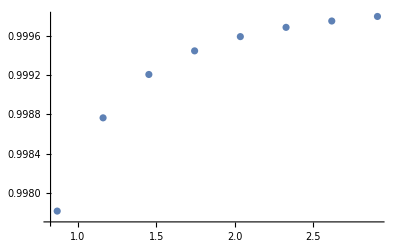

```mathematica
ListPlot[values2]
```

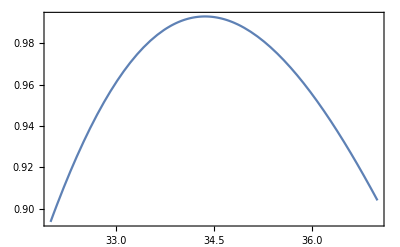

```mathematica
Plot[{Favf[b1,1,2]},{b1,32,37},Frame->True]
```

```mathematica
l=3;
n=3;
l1=N[Table[{f[k,l],k},{k,1,40}]]
l2=N[Table[{g[m,l],m},{m,1,40}]]
b1sync=Intersection[l1[[All,1]],l2[[All,1]],SameTest->(Floor[#1,.2]==Floor[#2,.2]&)]
```

{{0.-57.9589 ⅈ,1.},{48.9842,2.},{24.9415,3.},{17.4753,4.},{13.5858,5.},{11.1542,6.},{9.47729,7.},{8.24625,8.},{7.30213,9.},{6.55415,10.},{5.94646,11.},{5.44269,12.},{5.01813,13.},{4.65537,14.},{4.34176,15.},{4.06792,16.},{3.82669,17.},{3.61257,18.},{3.4212,19.},{3.24915,20.},{3.09362,21.},{2.95232,22.},{2.8234,23.},{2.70529,24.},{2.59668,25.},{2.49647,26.},{2.40371,27.},{2.31761,28.},{2.23748,29.},{2.16271,30.},{2.09277,31.},{2.02723,32.},{1.96567,33.},{1.90774,34.},{1.85313,35.},{1.80156,36.},{1.75279,37.},{1.70659,38.},{1.66277,39.},{1.62114,40.}}

{{0.-28.9794 ⅈ,1.},{24.4921,2.},{12.4708,3.},{8.73763,4.},{6.79289,5.},{5.5771,6.},{4.73865,7.},{4.12313,8.},{3.65107,9.},{3.27708,10.},{2.97323,11.},{2.72134,12.},{2.50907,13.},{2.32768,14.},{2.17088,15.},{2.03396,16.},{1.91335,17.},{1.80628,18.},{1.7106,19.},{1.62458,20.},{1.54681,21.},{1.47616,22.},{1.4117,23.},{1.35264,24.},{1.29834,25.},{1.24823,26.},{1.20186,27.},{1.15881,28.},{1.11874,29.},{1.08135,30.},{1.04639,31.},{1.01361,32.},{0.982834,33.},{0.95387,34.},{0.926566,35.},{0.900782,36.},{0.876396,37.},{0.853297,38.},{0.831384,39.},{0.81057,40.}}

{1.75279,1.96567,2.16271,2.31761,2.59668,2.70529,2.95232,3.24915,3.61257,4.06792,4.65537,5.44269}

```mathematica
Favf[b1_,m_,k_]:=1/7+2/21 Cos[m π]^2 Cos[(√(A^2+b1^2) n π)/(2 b1)]^2+4/21 Cos[k π] Cos[m π] Cos[(√(A^2+b1^2) n π)/(2 b1)] Cos[(√(4 A^2+b1^2) n π)/(2 b1)]+2/21 Cos[k π]^2 Cos[(√(4 A^2+b1^2) n π)/(2 b1)]^2+2/21 Cos[(√(4 A^2+b1^2) n π)/(2 b1)]^2 Sin[k π]^2+4/21 Cos[(√(A^2+b1^2) n π)/(2 b1)] Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[m π]+2/21 Cos[(√(A^2+b1^2) n π)/(2 b1)]^2 Sin[m π]^2-4/21 Cos[m π] Cos[n π] Cos[(√(A^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]-4/21 Cos[k π] Cos[n π] Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]+2/21 Cos[n π]^2 Sin[(n π)/2]^2-4/21 Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[(n π)/2] Sin[n π]-4/21 Cos[(√(A^2+b1^2) n π)/(2 b1)] Sin[m π] Sin[(n π)/2] Sin[n π]+2/21 Sin[(n π)/2]^2 Sin[n π]^2;
```

```mathematica
localMax1=FindMaximum[{Favf[b1,2,1],1.6<=b1<=1.8},{b1,1.7527923318174752}]
localMax2=FindMaximum[{Favf[b1,2,1],1.9<=b1<=2.0},{b1,1.9656680624350131}]
localMax3=FindMaximum[{Favf[b1,2,1],2.1<=b1<=2.2},{b1,2.1627050730699984}]
localMax4=FindMaximum[{Favf[b1,2,1],2.4<=b1<=2.65},{b1,2.59667823503079}]
localMax5=FindMaximum[{Favf[b1,1,1],2.6<=b1<=2.8},{b1,2.7052889374878464}]
localMax6=FindMaximum[{Favf[b1,2,1],2.9<=b1<=3.1},{b1,2.9523248647298153}]
localMax7=FindMaximum[{Favf[b1,1,1],3.0<=b1<=3.4},{b1,3.2491511244540736}]
localMax8=FindMaximum[{Favf[b1,2,1],3.5<=b1<=3.7},{b1,3.6125654832306324}]
localMax9=FindMaximum[{Favf[b1,1,1],3.8<=b1<=4.1},{b1,4.067916037321753}]
localMax10=FindMaximum[{Favf[b1,2,1],4.5<=b1<=4.8},{b1,4.655369428534006}]
localMax11=FindMaximum[{Favf[b1,1,1],5.35<=b1<=5.5},{b1,5.442688411332872}]
localMax12=FindMaximum[{Favf[b1,3,2],23<=b1<=26},{b1,24.94153162899184}]
```

{0.995567,{b1→1.70739}}

{0.994468,{b1→1.90885}}

{0.992903,{b1→2.16432}}

{0.990569,{b1→2.49895}}

{0.988947,{b1→2.70844}}

{0.986868,{b1→2.95642}}

{0.984146,{b1→3.2546}}

{0.980486,{b1→3.62003}}

{0.975406,{b1→4.07853}}

{0.968074,{b1→4.67119}}

{0.956952,{b1→5.46774}}

{0.999393,{b1→24.8842}}

```mathematica
tg1 = π/b1;
values3 ={ {localMax1[[1]],localMax1[[2]],tg1/.localMax1[[2]]},{localMax2[[1]],localMax2[[2]],tg1/.localMax2[[2]]},{localMax3[[1]],localMax3[[2]],tg1/.localMax3[[2]]},{localMax4[[1]],localMax4[[2]],tg1/.localMax4[[2]]},{localMax5[[1]],localMax5[[2]],tg1/.localMax5[[2]]},{localMax6[[1]],localMax6[[2]],tg1/.localMax6[[2]]},{localMax7[[1]],localMax7[[2]],tg1/.localMax7[[2]]},{localMax8[[1]],localMax8[[2]],tg1/.localMax8[[2]]},{localMax9[[1]],localMax9[[2]],tg1/.localMax9[[2]]},{localMax10[[1]],localMax10[[2]],tg1/.localMax10[[2]]},{localMax11[[1]],localMax11[[2]],tg1/.localMax11[[2]]}};
values4 ={ {tg1/.localMax1[[2]],localMax1[[1]]},{tg1/.localMax2[[2]],localMax2[[1]]},{tg1/.localMax3[[2]],localMax3[[1]]},{tg1/.localMax4[[2]],localMax4[[1]]},{tg1/.localMax5[[2]],localMax5[[1]]},{tg1/.localMax6[[2]],localMax6[[1]]},{tg1/.localMax7[[2]],localMax7[[1]]},{tg1/.localMax8[[2]],localMax8[[1]]},{tg1/.localMax9[[2]],localMax9[[1]]},{tg1/.localMax10[[2]],localMax10[[1]]},{tg1/.localMax11[[2]],localMax11[[1]]}};
```

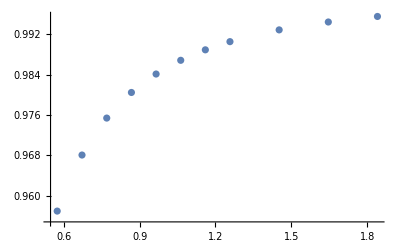

```mathematica
ListPlot[values4]
```

```mathematica
l=5;
n=5;
l1=N[Table[{f[k,l],k},{k,1,40}]]
l2=N[Table[{g[m,l],m},{m,1,40}]]
b1sync=Intersection[l1[[All,1]],l2[[All,1]],SameTest->(Floor[#1,.2]==Floor[#2,.2]&)]
```

{{0.-47.1351 ⅈ,1.},{0.-72. ⅈ,2.},{65.1265,3.},{34.5877,4.},{24.9415,5.},{19.8007,6.},{16.5179,7.},{14.2118,8.},{12.4916,9.},{11.1542,10.},{10.082,11.},{9.20191,12.},{8.46571,13.},{7.8403,14.},{7.30213,15.},{6.83394,16.},{6.42277,17.},{6.05872,18.},{5.73406,19.},{5.44269,20.},{5.17969,21.},{4.9411,22.},{4.72364,23.},{4.52461,24.},{4.34176,25.},{4.17318,26.},{4.01726,27.},{3.87261,28.},{3.73805,29.},{3.61257,30.},{3.49526,31.},{3.38535,32.},{3.28216,33.},{3.18509,34.},{3.09362,35.},{3.00726,36.},{2.9256,37.},{2.84828,38.},{2.77494,39.},{2.70529,40.}}

{{0.-23.5675 ⅈ,1.},{0.-36. ⅈ,2.},{32.5632,3.},{17.2938,4.},{12.4708,5.},{9.90034,6.},{8.25897,7.},{7.10588,8.},{6.2458,9.},{5.5771,10.},{5.04101,11.},{4.60095,12.},{4.23285,13.},{3.92015,14.},{3.65107,15.},{3.41697,16.},{3.21139,17.},{3.02936,18.},{2.86703,19.},{2.72134,20.},{2.58985,21.},{2.47055,22.},{2.36182,23.},{2.26231,24.},{2.17088,25.},{2.08659,26.},{2.00863,27.},{1.9363,28.},{1.86903,29.},{1.80628,30.},{1.74763,31.},{1.69267,32.},{1.64108,33.},{1.59255,34.},{1.54681,35.},{1.50363,36.},{1.4628,37.},{1.42414,38.},{1.38747,39.},{1.35264,40.}}

{2.77494,2.9256,3.18509,3.38535,3.49526,3.73805,3.87261,4.34176,4.72364,5.17969,5.44269,12.4916}

```mathematica
Favf[b1_,m_,k_]:=1/7+2/21 Cos[m π]^2 Cos[(√(A^2+b1^2) n π)/(2 b1)]^2+4/21 Cos[k π] Cos[m π] Cos[(√(A^2+b1^2) n π)/(2 b1)] Cos[(√(4 A^2+b1^2) n π)/(2 b1)]+2/21 Cos[k π]^2 Cos[(√(4 A^2+b1^2) n π)/(2 b1)]^2+2/21 Cos[(√(4 A^2+b1^2) n π)/(2 b1)]^2 Sin[k π]^2+4/21 Cos[(√(A^2+b1^2) n π)/(2 b1)] Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[m π]+2/21 Cos[(√(A^2+b1^2) n π)/(2 b1)]^2 Sin[m π]^2-4/21 Cos[m π] Cos[n π] Cos[(√(A^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]-4/21 Cos[k π] Cos[n π] Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[(n π)/2]+2/21 Cos[n π]^2 Sin[(n π)/2]^2-4/21 Cos[(√(4 A^2+b1^2) n π)/(2 b1)] Sin[k π] Sin[(n π)/2] Sin[n π]-4/21 Cos[(√(A^2+b1^2) n π)/(2 b1)] Sin[m π] Sin[(n π)/2] Sin[n π]+2/21 Sin[(n π)/2]^2 Sin[n π]^2;
```

```mathematica
localMax1=FindMaximum[{Favf[b1,1,1],12<=b1<=13},{b1,12.491602530470788}]
localMax2=FindMaximum[{Favf[b1,2,2],5<=b1<=6},{b1,5.442688411332872}]
localMax3=FindMaximum[{Favf[b1,1,2],4.8<=b1<=6},{b1,5.179692287280617}]
localMax4=FindMaximum[{Favf[b1,2,2],4.5<=b1<=5},{b1,4.723639381879511}]
localMax5=FindMaximum[{Favf[b1,1,2],4<=b1<=4.5},{b1,4.341763361919797}]
localMax6=FindMaximum[{Favf[b1,2,2],3.5<=b1<=4},{b1,3.8726098486081866}]
localMax7=FindMaximum[{Favf[b1,1,2],3.5<=b1<=3.9},{b1,3.738053747888389}]
localMax8=FindMaximum[{Favf[b1,2,2],3<=b1<=3.7},{b1,3.495255453243008}]
localMax9=FindMaximum[{Favf[b1,2,2],3<=b1<=4.1},{b1,3.3853470719184893}]
localMax10=FindMaximum[{Favf[b1,1,2],2.8<=b1<=3.5},{b1,3.1850924774674243}]
localMax11=FindMaximum[{Favf[b1,1,2],2.7<=b1<=3.5},{b1,2.9256048017882663}]
localMax12=FindMaximum[{Favf[b1,2,2],2<=b1<=3},{b1,2.774937940630782}]
```

{0.999908,{b1→12.4881}}

{0.88495,{b1→5.46713}}

{0.903691,{b1→4.95958}}

{0.918279,{b1→4.53892}}

{0.929836,{b1→4.18447}}

{0.939134,{b1→3.88168}}

{0.946719,{b1→3.61995}}

{0.962624,{b1→3.01156}}

{0.952983,{b1→3.39145}}

{0.958214,{b1→3.19019}}

{0.966375,{b1→2.85193}}

{0.978763,{b1→2.25488}}

```mathematica
tg1 = π/b1;
values5 ={ {localMax1[[1]],localMax1[[2]],tg1/.localMax1[[2]]},{localMax2[[1]],localMax2[[2]],tg1/.localMax2[[2]]},{localMax3[[1]],localMax3[[2]],tg1/.localMax3[[2]]},{localMax4[[1]],localMax4[[2]],tg1/.localMax4[[2]]},{localMax5[[1]],localMax5[[2]],tg1/.localMax5[[2]]},{localMax6[[1]],localMax6[[2]],tg1/.localMax6[[2]]},{localMax7[[1]],localMax7[[2]],tg1/.localMax7[[2]]},{localMax8[[1]],localMax8[[2]],tg1/.localMax8[[2]]},{localMax9[[1]],localMax9[[2]],tg1/.localMax9[[2]]},{localMax10[[1]],localMax10[[2]],tg1/.localMax10[[2]]},{localMax11[[1]],localMax11[[2]],tg1/.localMax11[[2]]}};
values6 ={ {tg1/.localMax1[[2]],localMax1[[1]]},{tg1/.localMax2[[2]],localMax2[[1]]},{tg1/.localMax3[[2]],localMax3[[1]]},{tg1/.localMax4[[2]],localMax4[[1]]},{tg1/.localMax5[[2]],localMax5[[1]]},{tg1/.localMax6[[2]],localMax6[[1]]},{tg1/.localMax7[[2]],localMax7[[1]]},{tg1/.localMax8[[2]],localMax8[[1]]},{tg1/.localMax9[[2]],localMax9[[1]]},{tg1/.localMax10[[2]],localMax10[[1]]},{tg1/.localMax11[[2]],localMax11[[1]]}};
```

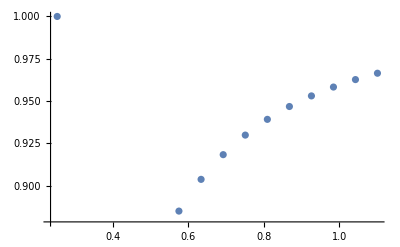

```mathematica
ListPlot[values6]
```

```mathematica
l=Join[values2,values4,values6]
l1=Select[l,#[[2]]>0.99&]
l2=l1/. {a_,b_}->{10*a,b}
```

{{2.90743,0.999802},{2.61638,0.999755},{2.32529,0.999691},{2.03414,0.999596},{1.74291,0.99945},{1.45153,0.999209},{1.15992,0.998766},{0.867827,0.997813},{1.84,0.995567},{1.6458,0.994468},{1.45154,0.992903},{1.25717,0.990569},{1.15992,0.988947},{1.06263,0.986868},{0.965278,0.984146},{0.867836,0.980486},{0.770275,0.975406},{0.672547,0.968074},{0.574569,0.956952},{0.251567,0.999908},{0.574633,0.88495},{0.633439,0.903691},{0.692146,0.918279},{0.750773,0.929836},{0.809339,0.939134},{0.867854,0.946719},{1.04318,0.962624},{0.926328,0.952983},{0.984768,0.958214},{1.10157,0.966375}}

{{2.90743,0.999802},{2.61638,0.999755},{2.32529,0.999691},{2.03414,0.999596},{1.74291,0.99945},{1.45153,0.999209},{1.15992,0.998766},{0.867827,0.997813},{1.84,0.995567},{1.6458,0.994468},{1.45154,0.992903},{1.25717,0.990569},{0.251567,0.999908}}

{{29.0743,0.999802},{26.1638,0.999755},{23.2529,0.999691},{20.3414,0.999596},{17.4291,0.99945},{14.5153,0.999209},{11.5992,0.998766},{8.67827,0.997813},{18.4,0.995567},{16.458,0.994468},{14.5154,0.992903},{12.5717,0.990569},{2.51567,0.999908}}

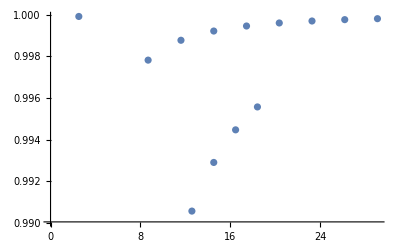

```mathematica
ListPlot[l2]
```

```mathematica
Export["file4.dat",l2,"Table"]
```

file4.dat